Polynomial Interpolation is the method of finding a polynomial p(x) such that for n+1 distinct points x_0,x_1,…, x_n and values f_i=f(x_i) for a given function, p(x_i)=f_i. In other words we are trying to find a polynomial that passes through n+1 distinct points. In general this can be accomplished with a degree n polynomial. In fact the degree n polynomial that interpolates a set of n+1 points is unique, that is for a given set of points, there is only one polynomial that interpolates those points. However there are several different ways of computing this polynomial, and some are more efficient than others.

### Lagrange Interpolation

Lagrange Interpolation is the original and most basic way of finding the interpolating polynomial.

```mathematica
(* define Subscript[x, 1],Subscript[x, 2],…,Subscript[x, n+1] in xd - stands for x data*)
xd;
(* define Subscript[f, 1],Subscript[f, 2],…,Subscript[f, n+1] in fd - stands for f data*)
fd;
n =Length[xd]-1; 
Subscript[l, i_][x_]:=(∏_(j=1)^(i-1) (x - xd[[j]])/(xd[[i]]-xd[[j]]) )(∏_(j=i+1)^(n+1) (x - xd[[j]])/(xd[[i]]-xd[[j]]));
p[x_]:=∑_(i=1)^(n+1) fd[[i]]Subscript[l, i][x];
```

Note that l_i(x) = 0 at x_j where j≠i and l_i(x_i)=1. Thus p(x_i) = f_i l_i(x_i)=f_i for all i.

#### Example

0.802463 x-0.851606 x^3+0.29613 x^5-0.0405035 x^7+0.00186503 x^9

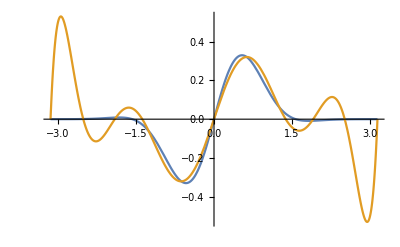

```mathematica
(* define Subscript[x, 1],Subscript[x, 2],…,Subscript[x, n+1] in xd - stands for x data*)
xd=Range[-π,π,π/5];
(* define Subscript[f, 1],Subscript[f, 2],…,Subscript[f, n+1] in fd - stands for f data*)
f[x_]:=ⅇ^(-x^2)Cos[x]*Sin[x];
fd=f[xd];
n =Length[xd]-1; 
Subscript[l, i_][x_]:=(∏_(j=1)^(i-1) (x - xd[[j]])/(xd[[i]]-xd[[j]]) )(∏_(j=i+1)^(n+1) (x - xd[[j]])/(xd[[i]]-xd[[j]]));
p[x_]:=∑_(i=1)^(n+1) fd[[i]]Subscript[l, i][x];
p[x]//FullSimplify//Expand//N
Plot[{f[x],p[x]},{x,-π,π}]
```

Note the large error near the ends of domain. This is known as Runge’s Phenomenon and occurs whenever the nodes are equally spaced. Inorder to combat this issue, Chebyshev nodes are often used instead of equally spaced nodes. See Chebyshev.nb for more information.

### Barycentric Formula

The Barycentric Formula is a more computationally efficient way of computing the polynomial interpolation. Requires that x_i are mutually distinct.

```mathematica
(* define Subscript[x, 1],Subscript[x, 2],…,Subscript[x, n+1] in xd - stands for x data*)
xd;
(* define Subscript[f, 1],Subscript[f, 2],…,Subscript[f, n+1] in fd - stands for f data*)
fd;
n =Length[xd]-1;
Subscript[λ, i_]:=(∏_(j=1)^(i-1) 1/(xd[[i]]-xd[[j]]))(∏_(j=i+1)^(n+1) 1/(xd[[i]]-xd[[j]]));
p[x_]:=(∑_(i=1)^(n+1) (Subscript[λ, i]/(x-xd[[i]])fd[[i]]))/(∑_(i=1)^(n+1) Subscript[λ, i]/(x - xd[[i]]))
```

#### Derivation

```mathematica
ω[x_]:=∏_(j=1)^(n+1) (x-xd[[j]]);
Subscript[l, i_][x_]:=Subscript[λ, i]/(x-xd[[i]])ω[x];
```

#### Example

```mathematica
(* define Subscript[x, 1],Subscript[x, 2],…,Subscript[x, n+1] in xd - stands for x data*)
xd=Range[-π,π,π/5];
(* define Subscript[f, 1],Subscript[f, 2],…,Subscript[f, n+1] in fd - stands for f data*)
f[x_]:=ⅇ^(-x^2)Cos[x]*Sin[x];
fd=f[xd];
n =Length[xd]-1;
Subscript[λ, i_]:=(∏_(j=1)^(i-1) 1/(xd[[i]]-xd[[j]]))(∏_(j=i+1)^(n+1) 1/(xd[[i]]-xd[[j]]));
p[x_]:=(∑_(i=1)^(n+1) (Subscript[λ, i]/(x-xd[[i]])*fd[[i]]))/(∑_(i=1)^(n+1) Subscript[λ, i]/(x - xd[[i]]))
p[x]//FullSimplify//Expand//N
Plot[{f[x],p[x]},{x,-π,π}]
```

0.802463 x-0.851606 x^3+0.29613 x^5-0.0405035 x^7+0.00186503 x^9

-Graphics-

### Newton’s Formula

#### Derivation

#### Example

### Hermite Interpolation

#### Derivation

#### Example